```mathematica
brick[z_Integer,n_Integer]:=Graphics[Text@Style[z,FontFamily->"Consolas",
FontSize->30-(1+Boole[n>12])(n-10),FontWeight->"Medium",White],
Background->If[z==0,White,RGBColor[z/n,0,1-z/n,(8 + 2 z/n)/10]]]
```

```mathematica
modularGrid[n_Integer]:=GraphicsGrid[Table[Mod[i j,n]~brick~n,{i,n},{j,n}],
Frame->False,Spacings->0]
```

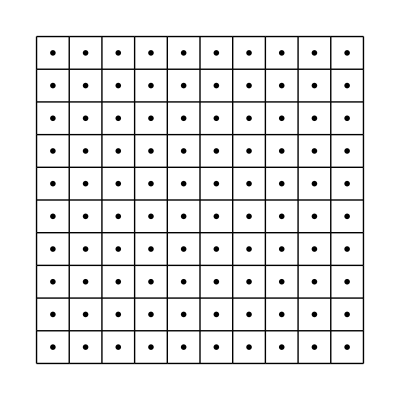

```mathematica
GraphicsGrid[Table[Graphics@Text@Style[i j,FontSize->24,
FontWeight->"Medium",FontFamily->"Consolas"],{i,10},{j,10}],Frame->All]
```

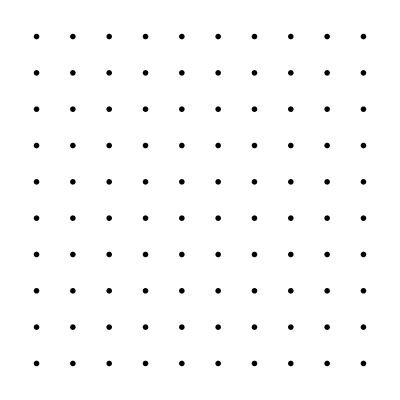

```mathematica
modularGrid[10]
```

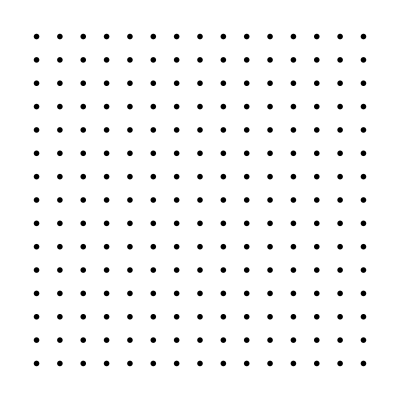

```mathematica
modularGrid[15]
```

```mathematica
modularArray[n_Integer]:=ArrayPlot[Table[Mod[i j,n],{i,n-1},{j,n-1}],
ColorFunction->(If[#==0,White,RGBColor[#/n,0,1-#/n,(8+2 #/n)/10]]&),
ColorFunctionScaling->False,Frame->False,ImageSize->Full]
```

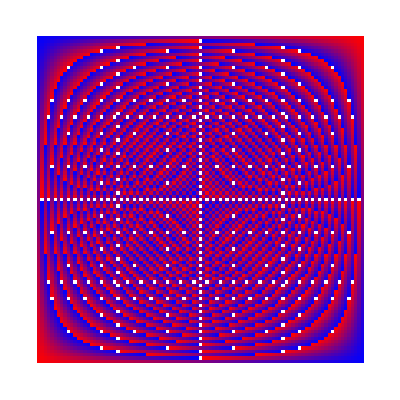

```mathematica
modularArray[100]
```

```mathematica
Animate[ArrayPlot[Table[Mod[i j,n],{i,n-1},{j,n-1}],
ColorFunction->(If[#==0,White,RGBColor[#/n,0,1-#/n,(8+2 #/n)/10]]&),
ColorFunctionScaling->False,Frame->False,ImageSize->Full],
{n,58,61,1},AnimationRunning->False]
```